# Rollups benchmarks

## Benchmarking exec units as a function of “update length”

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Reference protocol parameters (June 2023)

```mathematica
maxExSteps=10000000000;
maxExMem=14000000;
```

#### Import benchmark data

```mathematica
data=Import["rollupBench_2.csv","CSV"];
```

## Data analysis

### CPU

```mathematica
cpuData={#⟦1⟧,#⟦2⟧}&/@data
```

{{0,4150154154},{50,4509772574},{100,4866199304},{150,5225817724},{200,5582244454},{250,5941862874},{300,6298289604},{350,6657908024},{400,7014334754},{450,7373953174},{500,7730379904},{550,8089998324},{600,8446425054},{650,8806043474},{700,9162470204},{750,9522088624},{800,9878515354},{850,10238133774},{900,10594560504},{950,10954178924},{1000,11310605654}}

#### Data plot (CPU)

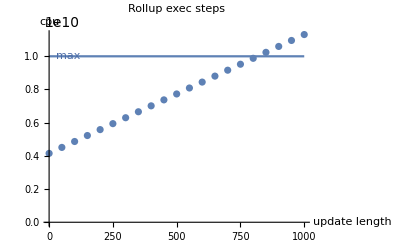

```mathematica
ListPlot[cpuData,PlotRange->All,
PlotLabel->"Rollup exec steps",AxesLabel->{"update length","cpu"}];
Plot[maxExSteps,{x,0,First@Last[cpuData]}];
Graphics[Text[Style["max",RGBColor[0.297856, 0.423621, 0.656168]],{75,maxExSteps},{0,-1}]];
cpuPlot=Show[%%%,%%,%]
```

#### Reaching maximum budget

```mathematica
FindRoot[Interpolation[cpuData][ul]==maxExSteps,{ul,40}]
```

{ul→816.896}

∴ CPU budget is exceded when update length is ≥ 817 .

#### Linear model

```mathematica
Fit[cpuData,{1,ul},ul]
```

4.15091×10^9+7.16045×10^6 ul

### Memory

```mathematica
memData={#⟦1⟧,#⟦3⟧}&/@data
```

{{0,2111935},{50,3197535},{100,4263135},{150,5348735},{200,6414335},{250,7499935},{300,8565535},{350,9651135},{400,10716735},{450,11802335},{500,12867935},{550,13953535},{600,15019135},{650,16104735},{700,17170335},{750,18255935},{800,19321535},{850,20407135},{900,21472735},{950,22558335},{1000,23623935}}

#### Data plot (memory)

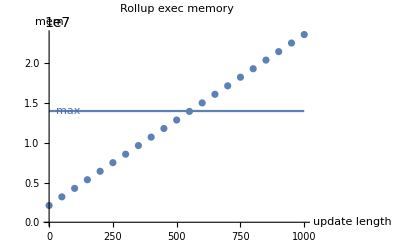

```mathematica
ListPlot[memData,PlotRange->All,
PlotLabel->"Rollup exec memory",AxesLabel->{"update length","mem"}];
Plot[maxExMem,{x,0,First@Last[cpuData]}];
Graphics[Text[Style["max",RGBColor[0.297856, 0.423621, 0.656168]],{75,maxExMem},{0,-1}]];
memPlot=Show[%%%,%%,%]
```

#### Reaching maximum budget

```mathematica
FindRoot[Interpolation[memData][ul]==maxExMem,{ul,40}]
```

{ul→552.174}

∴ Memory budget is exceded when update length is ≥ 553 .

#### Linear model

```mathematica
Fit[memData,{1,ul},ul]
```

2.1167×10^6+21512. ul

## Conclusion

To be within exec units budget, update length must be 552 or less.

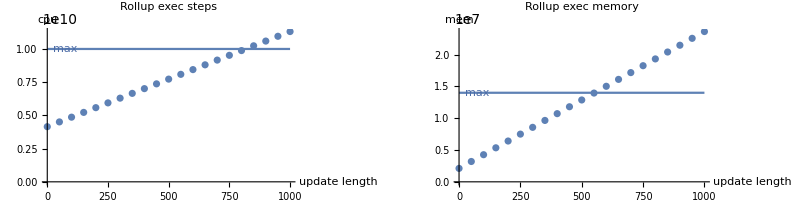

```mathematica
GraphicsRow[{cpuPlot,memPlot}]
```